```mathematica
(*1. Functions*)
```

```mathematica
f[x_]:=Sin[x]
```

```mathematica
f'[x]
(f[x])^2+(f'[x])^2
Integrate[f[x],x]
```

Cos[x]

Cos[x]^2+Sin[x]^2

-Cos[x]

```mathematica
(*2. Simplify*)
```

```mathematica
Simplify[%3]
```

1

```mathematica
(*3. Plotting Functions*)
```



-Graphics-

```mathematica
Plot[Sin[x],{x,0,2π}]
Plot[f[x],{x,0,2 π}]
```

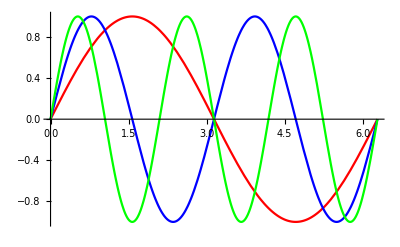

```mathematica
Plot[{f[x],f[2x],f[3x]},{x,0,2 π}, PlotStyle->{Red, Blue, Green}]
```

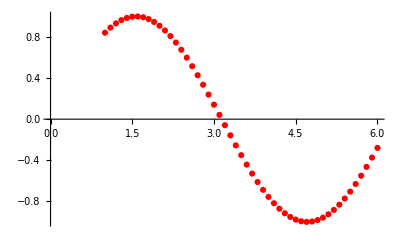

```mathematica
Table[{i,Sin[i]},{i,1,6,0.1}];
ListPlot[%,PlotStyle->Red]
```

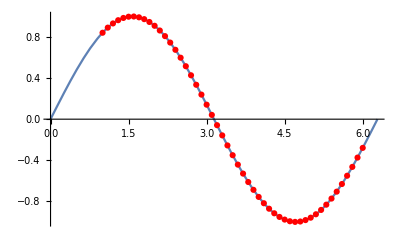

```mathematica
Show[{Plot[f[x],{x,0,2 π}],%10}]
```

```mathematica
(*4. Solving Differential Equations*)
```

{{y[x]→ⅇ^-x}}

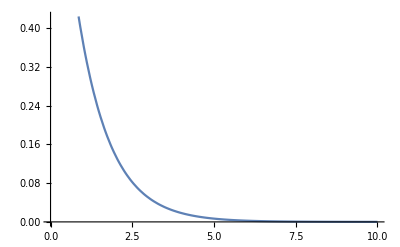

```mathematica
DSolve[{y'[x]==-y[x],y[0]==1},y[x],x]
Plot[y[x]/.%13,{x,0,10}]
```

{{y[x]→InterpolatingFunction[{{0., 10.}}, <>][x]}}

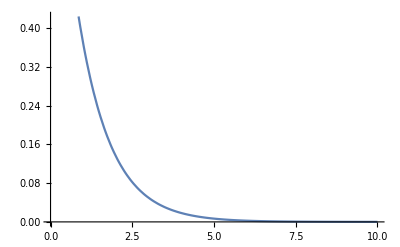

```mathematica
NDSolve[{y'[x]==-y[x],y[0]==1},y[x],{x,0,10}]
Plot[y[x]/.%15,{x,0,10}]
```

```mathematica
RSolve[{y[n+1]==(1-h)y[n], y[0]==1},y[n],n]
```

{{y[n]→(1-h)^n}}

```mathematica
Table[{h n, y[n]/.%17[[1]][[1]]},{n,0,100}];
```

```mathematica
R[t_]:=%23/.h->t
```

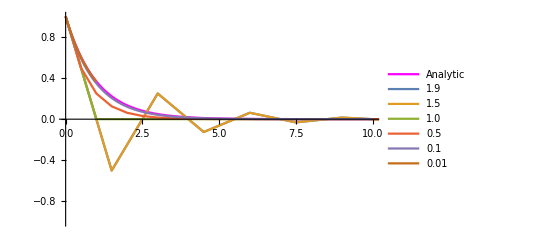

```mathematica
ListPlot[{R[1.5],R[1.5],R[1.0],R[0.5],R[0.1],R[0.01]},Joined->True,PlotLegends->{"1.9","1.5","1.0","0.5","0.1","0.01"}];
Show[Plot[y[x]/.%13,{x,0,10},PlotRange->{-1,1},PlotLegends->{"Analytic"}, PlotStyle->{Magenta}],%29]
```

```mathematica
sol1=DSolve[{y''[x]+3y'[x]+2y[x]==0,y[0]==1,y'[0]==1},y[x],x][[1]][[1]];
sol2=NDSolve[{y''[x]+3y'[x]+2y[x]==0,y[0]==1,y'[0]==1},y[x],{x,0,10}][[1]][[1]];
sol3=RSolve[{y[n+1](2+3h) + y[n]4(h+1)(h-1)+y[n-1](2-3h)==0, y[0]==1,y[1]-(4(1-h)(1+h)-y[1](2+3h))/(2-3h)==2h},y[n],n][[1]][[1]];
tab=Table[{h n, y[n]/.sol3},{n,0,1000}];
R2[t_]:=tab/.h->t;
```

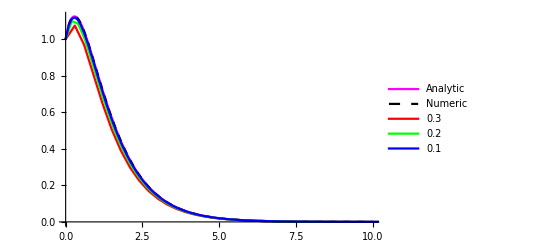

```mathematica
Show[{Plot[{y[x]/.sol1,y[x]/.sol2},{x,0,10},PlotLegends->{"Analytic", "Numeric"},PlotStyle->{Magenta,{Black,Dashed}}],ListPlot[{R2[0.3],R2[0.2],R2[0.1]},PlotRange->{0,1.5},PlotLegends->{"0.3","0.2","0.1"},Joined->True,PlotStyle->{Red, Green,Blue}]}]
```